### Fitting the nonlinear public goods game in a growing population far away from K to the in vitro data of Archetti et al., PNAS 2015

#### Original Data and ODE

```mathematica
serum=0.01{1,2,3,4,5,6,7,8,9,10};
initial=0.01{2.3,14.6,23.9,35.4,45.8,54.9,64.8,74.6,83.3,91,98.3};
final[1]=0.01{{3.5,4.07,4.0,3.5,3.4,4.0,3.7,3.5,3.7,3.7},{6.5,9.1,12.4,12.1,14.8,15.3,15.8,17.4,19.8,22.1},{12.4,15.8,15.5,18.5,24.1,28.4,30.6,31.4,31.4,35.37},{20.0,23.3,28.0,31.8,28.47,36.3,42.1,41.4,41.7,40.6},{23.6,29.2,37.4,37.8,42.00,47.8,51.2,51.6,53.5,50.4},{37.2,33.1,49.9,45.0,55.2,53.8,57.3,61.5,61.8,57.6},{37.2,41.6,45.8,57.5,64.0,60.9,66.34,65.5,70.3,75.5},{51.0,53.9,63.6,70.2,74.01,71.1,74.2,73.4,78.6,79.5},{67.0,74.9,80.9,80.8,82.5,83.6,86.1,87.3,88.6,89.2},{77.4,82.4,87.5,91.3,92.4,92.4,93.9,96.2,95.4,94.1},{96.4,99.6,99.28,99.7,99.5,99.3,99.8,99.96,99.9,99.9}};
final[2]=0.01{{3.6,4.1,3.6,3.6,3.5,3.52,4.0,3.8,3.9,3.8},{7.0,9.6,11.7,12.3,16.2,15.3,17.1,17.3,19.9,22.5},{11.7,15.6,14.4,17.7,21.5,26.6,28.1,30.9,31.2,35.5},{18.5,23.12,26.2,28.5,31.6,35.6,42.8,38.6,38.6,43.9},{23.3,28.5,36.5,37.7,37.2,45.6,46.0,49.3,55.7,52.7},{29.2,34.6,45.6,45.9,47.6,54.2,60.6,62.6,64.7,60.8},{33.9,39.5,51.8,56.4,60.4,62.0,63.1,64.6,71.8,77.2},{49.8,57.5,60.4,70.4,71.0,73.0,71.91,77.0,78.7,78.3},{68.9,74.1,79.6,81.5,82.6,85.8,85.2,87.0,87.6,88.4},{78.4,82.2,88.7,91.4,92.7,93.5,93.4,95.0,95.9,95.8},{96.4,99.3,99.4,99.5,99.7,99.2,99.70,100.2,99.70,99.8}};
final[3]=0.01{{3.4,3.7,3.8,3.8,3.7,3.4,3.7,4.0,3.7,3.6},{6.2,9.7,11.9,12.9,15.92,16.0,16.4,17.6,19.6,22.4},{12.2,14.8,15.9,18.9,24.5,26.5,29.3,32.1,32.8,34.2},{20.2,26.9,26.87,31.1,31.1,36.0,42.6,40.2,42.1,44.0},{25.3,27.2,33.1,40.1,39.4,45.4,47.4,52.34,50.2,51.9},{36.3,34.0,49.9,43.5,48.8,51.7,54.7,58.1,58.6,64.6},{30.7,37.3,48.4,55.2,61.4,63.0,66.1,66.6,75.0,77.6},{50.92,57.3,59.1,70.5,74.3,72.6,74.5,75.2,75.4,80.5},{66.7,74.0,81.2,82.80,85.1,85.3,86.1,86.6,88.0,88.3},{78.6,83.7,88.9,90.9,91.1,93.4,94.9,95.5,95.6,95.9},{96.6,99.4,99.5,99.5,99.3,99.4,99.8,100.1,99.7,100.1}};final[4]=0.01{{3.8,3.8,3.7,4.0,3.5,3.4,3.8,3.4,3.5,3.4},{6.0,9.9,11.4,12.84,15.6,16.4,16.8,18.4,19.1,22.11},{12.1,15.9,15.14,17.9,24.7,27.7,28.8,33.3,33.4,36.81},{19.96,23.5,24.4,29.8,29.6,34.7,41.6,43.2,42.1,41.0},{24.1,24.7,33.0,39.4,41.7,47.2,52.84,48.2,50.3,53.3},{28.2,37.5,50.1,53.0,47.71,56.75,51.92,60.5,60.34,61.3},{30.6,35.9,50.9,52.6,61.4,63.9,66.0,70.6,72.2,78.0},{51.6,54.5,62.8,71.7,70.5,74.0,76.7,74.1,79.6,77.2},{66.5,74.1,81.6,83.2,83.1,86.0,86.33,87.5,89.3,87.5},{78.3,82.7,88.4,92.0,92.5,92.6,94.9,95.6,94.3,94.5},{96.6,99.7,99.1,99.5,99.1,99.6,99.69,99.7,99.6,99.6}};
e=1;
i=initial;
Ly=initial//Length;
Ls=10;
MedianData=Table[
f=Median[{final[1],final[2],final[3],final[4]}];
(*(1-f⟦#,s⟧)-(1-i⟦#⟧)&/@Range[1,Ly,1]*)
{(1-f⟦#,s⟧),(1-i⟦#⟧)}&/@Range[1,Ly,1]
,{s,1,10}
];

fitData[e_]:=Flatten[
Table[
f=final[e];
{1-i⟦#⟧,serum⟦s⟧,(1-f⟦#,s⟧)}&/@Range[1,Ly,1]
,{s,1,10}
]
,1];

fitData[1]
```

{{0.977,0.01,0.965},{0.854,0.01,0.935},{0.761,0.01,0.876},{0.646,0.01,0.8},{0.542,0.01,0.764},{0.451,0.01,0.628},{0.352,0.01,0.628},{0.254,0.01,0.49},{0.167,0.01,0.33},{0.09,0.01,0.226},{0.017,0.01,0.036},{0.977,0.02,0.9593},{0.854,0.02,0.909},{0.761,0.02,0.842},{0.646,0.02,0.767},{0.542,0.02,0.708},{0.451,0.02,0.669},{0.352,0.02,0.584},{0.254,0.02,0.461},{0.167,0.02,0.251},{0.09,0.02,0.176},{0.017,0.02,0.004},{0.977,0.03,0.96},{0.854,0.03,0.876},{0.761,0.03,0.845},{0.646,0.03,0.72},{0.542,0.03,0.626},{0.451,0.03,0.501},{0.352,0.03,0.542},{0.254,0.03,0.364},{0.167,0.03,0.191},{0.09,0.03,0.125},{0.017,0.03,0.0072},{0.977,0.04,0.965},{0.854,0.04,0.879},{0.761,0.04,0.815},{0.646,0.04,0.682},{0.542,0.04,0.622},{0.451,0.04,0.55},{0.352,0.04,0.425},{0.254,0.04,0.298},{0.167,0.04,0.192},{0.09,0.04,0.087},{0.017,0.04,0.003},{0.977,0.05,0.966},{0.854,0.05,0.852},{0.761,0.05,0.759},{0.646,0.05,0.7153},{0.542,0.05,0.58},{0.451,0.05,0.448},{0.352,0.05,0.36},{0.254,0.05,0.2599},{0.167,0.05,0.175},{0.09,0.05,0.076},{0.017,0.05,0.005},{0.977,0.06,0.96},{0.854,0.06,0.847},{0.761,0.06,0.716},{0.646,0.06,0.637},{0.542,0.06,0.522},{0.451,0.06,0.462},{0.352,0.06,0.391},{0.254,0.06,0.289},{0.167,0.06,0.164},{0.09,0.06,0.076},{0.017,0.06,0.007},{0.977,0.07,0.963},{0.854,0.07,0.842},{0.761,0.07,0.694},{0.646,0.07,0.579},{0.542,0.07,0.488},{0.451,0.07,0.427},{0.352,0.07,0.3366},{0.254,0.07,0.258},{0.167,0.07,0.139},{0.09,0.07,0.061},{0.017,0.07,0.002},{0.977,0.08,0.965},{0.854,0.08,0.826},{0.761,0.08,0.686},{0.646,0.08,0.586},{0.542,0.08,0.484},{0.451,0.08,0.385},{0.352,0.08,0.345},{0.254,0.08,0.266},{0.167,0.08,0.127},{0.09,0.08,0.038},{0.017,0.08,0.0004},{0.977,0.09,0.963},{0.854,0.09,0.802},{0.761,0.09,0.686},{0.646,0.09,0.583},{0.542,0.09,0.465},{0.451,0.09,0.382},{0.352,0.09,0.297},{0.254,0.09,0.214},{0.167,0.09,0.114},{0.09,0.09,0.046},{0.017,0.09,0.001},{0.977,0.1,0.963},{0.854,0.1,0.779},{0.761,0.1,0.6463},{0.646,0.1,0.594},{0.542,0.1,0.496},{0.451,0.1,0.424},{0.352,0.1,0.245},{0.254,0.1,0.205},{0.167,0.1,0.108},{0.09,0.1,0.059},{0.017,0.1,0.001}}

```mathematica
Clear[data,nlm,e,i,Ly,Ls,y,t,y0,n,β,σ,α,κ,s]
α=.;
sol=ParametricNDSolve[
{
y'[t]==y[t](1-y[t])α((1+Exp[-σ s])/(1+Exp[-σ s-β(1/n+(n-1)/n y[t])])-(1+Exp[-σ s])/(1+Exp[-σ s-β(n-1)/n y[t]])-κ),y[0]==y0
}
,y,{t,0,100},{y0,n,β,σ, s,α,κ}
];

e=1;
i=initial;
Ly=initial//Length;
Ls=10;
data[e_]:=Flatten[
Table[
f=final[e];
{1-i⟦#⟧,(*serum⟦s⟧,*)(1-f⟦#,s⟧)}&/@Range[1,Ly,1]
,{s,1,10}
]
,1];

fD=Flatten[Take[data[#],11]&/@Range[1,4,1],1];
AppendTo[fD,{1.,1.0}];
AppendTo[fD,{0.,0.0}]
nlm=NonlinearModelFit[fD,y[x1,n,β,σ,1,1.0,0.5][4]/.sol,{β,n,σ},{x1}];

nlm["ParameterTable"]
```

{{0.977,0.965},{0.854,0.935},{0.761,0.876},{0.646,0.8},{0.542,0.764},{0.451,0.628},{0.352,0.628},{0.254,0.49},{0.167,0.33},{0.09,0.226},{0.017,0.036},{0.977,0.964},{0.854,0.93},{0.761,0.883},{0.646,0.815},{0.542,0.767},{0.451,0.708},{0.352,0.661},{0.254,0.502},{0.167,0.311},{0.09,0.216},{0.017,0.036},{0.977,0.966},{0.854,0.938},{0.761,0.878},{0.646,0.798},{0.542,0.747},{0.451,0.637},{0.352,0.693},{0.254,0.4908},{0.167,0.333},{0.09,0.214},{0.017,0.034},{0.977,0.962},{0.854,0.94},{0.761,0.879},{0.646,0.8004},{0.542,0.759},{0.451,0.718},{0.352,0.694},{0.254,0.484},{0.167,0.335},{0.09,0.217},{0.017,0.034},{1.,1.},{0.,0.}}

| Estimate | Standard Error | t-Statistic | P-Value
β | 2.51187 | 0.213118 | 11.7863 | 4.68429×10^-15
n | 3.33106 | 0.51738 | 6.43831 | 8.4173×10^-8
σ | -1.15213 | 0.109442 | -10.5273 | 1.77309×10^-13

#### Parametric NDSolve

```mathematica
sol=ParametricNDSolve[
{
y'[t]==y[t](1-y[t])α((1+Exp[-σ s])/(1+Exp[-σ s-β(1/n+(n-1)/n y[t])])-(1+Exp[-σ s])/(1+Exp[-σ s-β(n-1)/n y[t]])-κ),y[0]==y0
}
,y,{t,0,100},{y0,n,β,σ, s,α,κ}
];
Manipulate[
Plot[
(y[y0,n,β,σ,-1,1.0,κ][4]/.sol)-y0
,{y0,0,1}
,Frame->True
,PlotRange->{{-0.05,1.05},Automatic}
,Filling->Axis
]
,{{n,4},1,11,0.5}
,{{κ,0.25},0,1,0.01}
,{{σ,0.1},-5,5,0.01}
,{{β,2.1},0,5,0.01}
]
```

ParametricNDSolve::fpct: Too many parameters in {y0,n,β,σ,α,κ} to be filled from {0.0000204286,4.,3.89,0.84,-1,1.,0.28}.

ParametricNDSolve::fpct: Too many parameters in {y0,n,β,σ,α,κ} to be filled from {0.0000204286,4.,3.89,0.84,-1.,1.,0.28}.

ParametricNDSolve::fpct: Too many parameters in {y0,n,β,σ,α,κ} to be filled from {0.0204286,4.,3.89,0.84,-1,1.,0.28}.

General::stop: Further output of ParametricNDSolve::fpct will be suppressed during this calculation.

ParametricNDSolve::fpct: Too many parameters in {y0,n,β,σ,α,κ} to be filled from {0.0000204286,4.,3.89,0.84,-1,1.,0.28}.

ParametricNDSolve::fpct: Too many parameters in {y0,n,β,σ,α,κ} to be filled from {0.0000204286,4.,3.89,0.84,-1.,1.,0.28}.

ParametricNDSolve::fpct: Too many parameters in {y0,n,β,σ,α,κ} to be filled from {0.0204286,4.,3.89,0.84,-1,1.,0.28}.

General::stop: Further output of ParametricNDSolve::fpct will be suppressed during this calculation.

```mathematica
d=MedianData⟦1⟧
L=Length[d]

sol=ParametricNDSolve[
{
y'[t]==y[t](1-y[t])α((1+Exp[σ])/(1+Exp[σ-β(1/n+(n-1)/n y[t])])-(1+Exp[σ])/(1+Exp[σ-β(n-1)/n y[t]])-κ),y[0]==y0
}
,y,{t,0,100},{y0,n,β,σ, α,κ}
];
Manipulate[
ListPlot[
{
{d⟦#,1⟧,(y[d⟦#,1⟧,n,β,σ,1.0,κ][4]/.sol)}&/@Range[1,L,1]
,
{d⟦#,1⟧,d⟦#,2⟧}&/@Range[1,L,1]
}
,Frame->True
,PlotRange->{{-0.05,1.05},Automatic}
,PlotStyle->{Red,Black}
]
,{{n,4},1,101,0.5}
,{{κ,0.25},0,1,0.01}
,{{σ,0.1},-5,5,0.01}
,{{β,2.1},0,5,0.01}
]
```

{{0.9645,0.977},{0.9365,0.854},{0.8785,0.761},{0.8002,0.646},{0.7615,0.542},{0.6725,0.451},{0.677,0.352},{0.4904,0.254},{0.3315,0.167},{0.2165,0.09},{0.035,0.017}}

11

### Independently fitting β,σ for every Serum Concentration

#### data

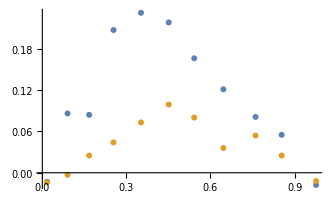

```mathematica
serum=0.01{1,2,3,4,5,6,7,8,9,10};
initial=0.01{2.3,14.6,23.9,35.4,45.8,54.9,64.8,74.6,83.3,91,98.3};
final[1]=0.01{{3.5,4.07,4.0,3.5,3.4,4.0,3.7,3.5,3.7,3.7},{6.5,9.1,12.4,12.1,14.8,15.3,15.8,17.4,19.8,22.1},{12.4,15.8,15.5,18.5,24.1,28.4,30.6,31.4,31.4,35.37},{20.0,23.3,28.0,31.8,28.47,36.3,42.1,41.4,41.7,40.6},{23.6,29.2,37.4,37.8,42.00,47.8,51.2,51.6,53.5,50.4},{37.2,33.1,49.9,45.0,55.2,53.8,57.3,61.5,61.8,57.6},{37.2,41.6,45.8,57.5,64.0,60.9,66.34,65.5,70.3,75.5},{51.0,53.9,63.6,70.2,74.01,71.1,74.2,73.4,78.6,79.5},{67.0,74.9,80.9,80.8,82.5,83.6,86.1,87.3,88.6,89.2},{77.4,82.4,87.5,91.3,92.4,92.4,93.9,96.2,95.4,94.1},{96.4,99.6,99.28,99.7,99.5,99.3,99.8,99.96,99.9,99.9}};
final[2]=0.01{{3.6,4.1,3.6,3.6,3.5,3.52,4.0,3.8,3.9,3.8},{7.0,9.6,11.7,12.3,16.2,15.3,17.1,17.3,19.9,22.5},{11.7,15.6,14.4,17.7,21.5,26.6,28.1,30.9,31.2,35.5},{18.5,23.12,26.2,28.5,31.6,35.6,42.8,38.6,38.6,43.9},{23.3,28.5,36.5,37.7,37.2,45.6,46.0,49.3,55.7,52.7},{29.2,34.6,45.6,45.9,47.6,54.2,60.6,62.6,64.7,60.8},{33.9,39.5,51.8,56.4,60.4,62.0,63.1,64.6,71.8,77.2},{49.8,57.5,60.4,70.4,71.0,73.0,71.91,77.0,78.7,78.3},{68.9,74.1,79.6,81.5,82.6,85.8,85.2,87.0,87.6,88.4},{78.4,82.2,88.7,91.4,92.7,93.5,93.4,95.0,95.9,95.8},{96.4,99.3,99.4,99.5,99.7,99.2,99.70,100.2,99.70,99.8}};
final[3]=0.01{{3.4,3.7,3.8,3.8,3.7,3.4,3.7,4.0,3.7,3.6},{6.2,9.7,11.9,12.9,15.92,16.0,16.4,17.6,19.6,22.4},{12.2,14.8,15.9,18.9,24.5,26.5,29.3,32.1,32.8,34.2},{20.2,26.9,26.87,31.1,31.1,36.0,42.6,40.2,42.1,44.0},{25.3,27.2,33.1,40.1,39.4,45.4,47.4,52.34,50.2,51.9},{36.3,34.0,49.9,43.5,48.8,51.7,54.7,58.1,58.6,64.6},{30.7,37.3,48.4,55.2,61.4,63.0,66.1,66.6,75.0,77.6},{50.92,57.3,59.1,70.5,74.3,72.6,74.5,75.2,75.4,80.5},{66.7,74.0,81.2,82.80,85.1,85.3,86.1,86.6,88.0,88.3},{78.6,83.7,88.9,90.9,91.1,93.4,94.9,95.5,95.6,95.9},{96.6,99.4,99.5,99.5,99.3,99.4,99.8,100.1,99.7,100.1}};final[4]=0.01{{3.8,3.8,3.7,4.0,3.5,3.4,3.8,3.4,3.5,3.4},{6.0,9.9,11.4,12.84,15.6,16.4,16.8,18.4,19.1,22.11},{12.1,15.9,15.14,17.9,24.7,27.7,28.8,33.3,33.4,36.81},{19.96,23.5,24.4,29.8,29.6,34.7,41.6,43.2,42.1,41.0},{24.1,24.7,33.0,39.4,41.7,47.2,52.84,48.2,50.3,53.3},{28.2,37.5,50.1,53.0,47.71,56.75,51.92,60.5,60.34,61.3},{30.6,35.9,50.9,52.6,61.4,63.9,66.0,70.6,72.2,78.0},{51.6,54.5,62.8,71.7,70.5,74.0,76.7,74.1,79.6,77.2},{66.5,74.1,81.6,83.2,83.1,86.0,86.33,87.5,89.3,87.5},{78.3,82.7,88.4,92.0,92.5,92.6,94.9,95.6,94.3,94.5},{96.6,99.7,99.1,99.5,99.1,99.6,99.69,99.7,99.6,99.6}};
e=1;
i=initial;
Ly=initial//Length;
Ls=10;
MedianData=Table[
f=Median[{final[1],final[2],final[3],final[4]}];
(*(1-f⟦#,s⟧)-(1-i⟦#⟧)&/@Range[1,Ly,1]*)
{(1-f⟦#,s⟧),(1-i⟦#⟧)}&/@Range[1,Ly,1]
,{s,1,10}
];

fitData[e_,s_]:=Module[{f},
f=final[e];
{serum⟦s⟧,
{1-i⟦#⟧,(1-f⟦#,s⟧)}&/@Range[1,Ly,1]
}
]
Clear[fd]
fd[ser_]:=Flatten[fitData[#,ser]⟦2⟧&/@Range[1,4,1],1]

ListPlot[
Table[
{fd[s]⟦#,1⟧,fd[s]⟦#,2⟧-fd[s]⟦#,1⟧}&/@Range[1,Ly,1]
,{s,2,4,2}]
]
```

#### fit

```mathematica
(*Clear[data,fit,nlm,y,t,y0,n,β,σ,α,κ,s]*)
Clear[β,σ,κ,n,y0,s];
serum=0.01{1,2,3,4,5,6,7,8,9,10};
initial=0.01{2.3,14.6,23.9,35.4,45.8,54.9,64.8,74.6,83.3,91,98.3};
final[1]=0.01{{3.5,4.07,4.0,3.5,3.4,4.0,3.7,3.5,3.7,3.7},{6.5,9.1,12.4,12.1,14.8,15.3,15.8,17.4,19.8,22.1},{12.4,15.8,15.5,18.5,24.1,28.4,30.6,31.4,31.4,35.37},{20.0,23.3,28.0,31.8,28.47,36.3,42.1,41.4,41.7,40.6},{23.6,29.2,37.4,37.8,42.00,47.8,51.2,51.6,53.5,50.4},{37.2,33.1,49.9,45.0,55.2,53.8,57.3,61.5,61.8,57.6},{37.2,41.6,45.8,57.5,64.0,60.9,66.34,65.5,70.3,75.5},{51.0,53.9,63.6,70.2,74.01,71.1,74.2,73.4,78.6,79.5},{67.0,74.9,80.9,80.8,82.5,83.6,86.1,87.3,88.6,89.2},{77.4,82.4,87.5,91.3,92.4,92.4,93.9,96.2,95.4,94.1},{96.4,99.6,99.28,99.7,99.5,99.3,99.8,99.96,99.9,99.9}};
final[2]=0.01{{3.6,4.1,3.6,3.6,3.5,3.52,4.0,3.8,3.9,3.8},{7.0,9.6,11.7,12.3,16.2,15.3,17.1,17.3,19.9,22.5},{11.7,15.6,14.4,17.7,21.5,26.6,28.1,30.9,31.2,35.5},{18.5,23.12,26.2,28.5,31.6,35.6,42.8,38.6,38.6,43.9},{23.3,28.5,36.5,37.7,37.2,45.6,46.0,49.3,55.7,52.7},{29.2,34.6,45.6,45.9,47.6,54.2,60.6,62.6,64.7,60.8},{33.9,39.5,51.8,56.4,60.4,62.0,63.1,64.6,71.8,77.2},{49.8,57.5,60.4,70.4,71.0,73.0,71.91,77.0,78.7,78.3},{68.9,74.1,79.6,81.5,82.6,85.8,85.2,87.0,87.6,88.4},{78.4,82.2,88.7,91.4,92.7,93.5,93.4,95.0,95.9,95.8},{96.4,99.3,99.4,99.5,99.7,99.2,99.70,100.2,99.70,99.8}};
final[3]=0.01{{3.4,3.7,3.8,3.8,3.7,3.4,3.7,4.0,3.7,3.6},{6.2,9.7,11.9,12.9,15.92,16.0,16.4,17.6,19.6,22.4},{12.2,14.8,15.9,18.9,24.5,26.5,29.3,32.1,32.8,34.2},{20.2,26.9,26.87,31.1,31.1,36.0,42.6,40.2,42.1,44.0},{25.3,27.2,33.1,40.1,39.4,45.4,47.4,52.34,50.2,51.9},{36.3,34.0,49.9,43.5,48.8,51.7,54.7,58.1,58.6,64.6},{30.7,37.3,48.4,55.2,61.4,63.0,66.1,66.6,75.0,77.6},{50.92,57.3,59.1,70.5,74.3,72.6,74.5,75.2,75.4,80.5},{66.7,74.0,81.2,82.80,85.1,85.3,86.1,86.6,88.0,88.3},{78.6,83.7,88.9,90.9,91.1,93.4,94.9,95.5,95.6,95.9},{96.6,99.4,99.5,99.5,99.3,99.4,99.8,100.1,99.7,100.1}};final[4]=0.01{{3.8,3.8,3.7,4.0,3.5,3.4,3.8,3.4,3.5,3.4},{6.0,9.9,11.4,12.84,15.6,16.4,16.8,18.4,19.1,22.11},{12.1,15.9,15.14,17.9,24.7,27.7,28.8,33.3,33.4,36.81},{19.96,23.5,24.4,29.8,29.6,34.7,41.6,43.2,42.1,41.0},{24.1,24.7,33.0,39.4,41.7,47.2,52.84,48.2,50.3,53.3},{28.2,37.5,50.1,53.0,47.71,56.75,51.92,60.5,60.34,61.3},{30.6,35.9,50.9,52.6,61.4,63.9,66.0,70.6,72.2,78.0},{51.6,54.5,62.8,71.7,70.5,74.0,76.7,74.1,79.6,77.2},{66.5,74.1,81.6,83.2,83.1,86.0,86.33,87.5,89.3,87.5},{78.3,82.7,88.4,92.0,92.5,92.6,94.9,95.6,94.3,94.5},{96.6,99.7,99.1,99.5,99.1,99.6,99.69,99.7,99.6,99.6}};
e=1;
i=initial;
Ly=initial//Length;
Ls=10;
fitData[e_,s_]:=Module[{f},
f=final[e];
{serum⟦s⟧,
{1-i⟦#⟧,(1-f⟦#,s⟧)}&/@Range[1,Ly,1]
}
]
Clear[fd]
fd[ser_]:=Flatten[fitData[#,ser]⟦2⟧&/@Range[1,4,1],1]
fitting[nn_,ser_]:=Module[
{sol,d,L,cost,nlm,βfitted,σfitted},
Clear[β,σ,κ,n,y0];
sol=ParametricNDSolve[
{
y'[t]==y[t](1-y[t])α((1+Exp[σ])/(1+Exp[σ-β(1/n+(n-1)/n y[t])])-(1+Exp[σ])/(1+Exp[σ-β(n-1)/n y[t]])-κ),y[0]==y0
}
,y,{t,0,100},{y0,n,β,σ,α,κ}
];

d=fd[ser];
L=Length[d];
cost=0.25;
nlm=NonlinearModelFit[d,y[x1,nn,β,σ,1.0,cost][4]/.sol,{β,σ},{x1}];
(* nlm["ParameterTable"] *)
βfitted=nlm["ParameterTableEntries"]⟦1,1⟧;
σfitted=nlm["ParameterTableEntries"]⟦2,1⟧;

(*ListPlot[
{
{d⟦#,1⟧,(y[d⟦#,1⟧,n,βfitted,σfitted,1.0,cost][4]/.sol)}&/@Range[1,L,1]
,
{d⟦#,1⟧,d⟦#,2⟧}&/@Range[1,L,1]
}
,Frame->True
,PlotRange->{{-0.05,1.05},Automatic}
,PlotStyle->{Red,Black}
]*)

{βfitted,σfitted}
]

Table[
fitting[23,s]
,{s,1,10,1}
]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

{{4.8496,2.34727},{4.66492,2.23863},{4.2724,2.05372},{3.87197,2.0008},{3.73733,1.90713},{3.82834,1.72243},{3.80112,1.57347},{3.61678,1.51393},{3.14884,1.49956},{3.20151,1.36751}}

#### Some other use of data

n=4...40 in steps of 1

```mathematica
T={{{2.26300676208,0.9887464703935777},{2.547546506096727,1.1431333536857171},{2.792929268853819,1.2740073585986973},{3.0082743770748026,1.3879079043991298},{3.1999270740053576,1.4888784051171986},{3.3725631836151173,1.5796051034501397},{3.5296198949241777,1.6620088939838245},{3.673753686094863,1.737499334430698},{3.8069983301445665,1.8071579691593413},{3.930965069717773,1.8718269548568218},{4.046924377855905,1.932180168641865},{4.155900034343258,1.9887637667248275},{4.258715082898994,2.0420280947985834},{4.356047826637887,2.092347775530358},{4.448386153446217,2.1400447518181123},{4.536203738427296,2.1853859043790207},{4.619994570829498,2.2285864577250356},{4.699918953679807,2.2698612681357067},{4.776372452310498,2.3093731913449984},{4.849595959512235,2.3472657912992454},{4.919579287994667,2.383695810078557},{4.98667307724713,2.4187602621697595},{5.05101556278874,2.452564116956845},{5.112467150925023,2.4852176641709893},{5.171864766150667,2.516759614025805},{5.228702870662557,2.5473000244110757},{5.2833150760880585,2.5768945252121993},{5.335608800490289,2.605616691635131},{5.385960868049195,2.633503930345892},{5.434325354997291,2.660614418101742},{5.480904266016828,2.6869889388324766},{5.525702217572224,2.712677839345612},{5.568646338462267,2.7377320142178876},{5.610397304617062,2.7621461290081504},{5.651049418252697,2.785951525255895},{5.690189423019511,2.8092210976180914},{5.72829389477047,2.8319515566320517}},{{2.1228244476522034,0.9060946648429522},{2.40066312472927,1.0564100535343406},{2.6409062118299347,1.1843119715790786},{2.851941233979949,1.2959716140981967},{3.0402837466848127,1.3950191806719328},{3.2100560504580558,1.4841302323771826},{3.364786865744808,1.5650747973842793},{3.506894680225984,1.639250460429151},{3.6383023327491433,1.7077096368108469},{3.7605853182258144,1.7712693616787372},{3.8749115748905707,1.8305959704091708},{3.982282105268139,1.8862224857269634},{4.083505910827203,1.9385888008297067},{4.179249686765186,1.988062730382141},{4.270074668164605,2.034952912935204},{4.356457656317704,2.0795211276716974},{4.438734838097778,2.1220011971366515},{4.51745419093005,2.162560093913443},{4.592732505583795,2.2013915139397473},{4.6649199459192365,2.2386319304859974},{4.734254146253293,2.2744107026799543},{4.800863532569926,2.3088491923544234},{4.8650312673994405,2.3420400186622956},{4.926918346926688,2.3740739914082836},{4.986638379037669,2.405035429758214},{5.044478188292564,2.4349847794552986},{5.100284808606493,2.464011953642074},{5.154495051958117,2.4921476617485845},{5.206930827285784,2.5194719672448875},{5.25790544921152,2.546014549742466},{5.3072522009744,2.5718399555572953},{5.355624443097891,2.5969472497344626},{5.402524238347959,2.6214168624320946},{5.448536978278667,2.6452400786138086},{5.492947227844657,2.668522912315293},{5.5365313140550105,2.6912262841825263},{5.579056858345234,2.713405807648059}},{{1.7746416437124213,0.836278282366694},{2.040881870072201,0.9642878530784037},{2.272388911668628,1.0766575028628977},{2.4771163843800554,1.176558177503201},{2.660590537343451,1.2663671530101885},{2.826818765067896,1.3478671739776544},{2.9787935365388933,1.422425351508541},{3.1187873465528955,1.4911060276017287},{3.2485686864888454,1.554758192464973},{3.36955478048261,1.6140570731429749},{3.4828400685355376,1.6695631403566673},{3.5895580214921585,1.7216910157292284},{3.6901046321806166,1.7708970413078389},{3.785560788329712,1.8174094938799952},{3.8761990748644295,1.8615584107454752},{3.962503862220517,1.9035687021431944},{4.044980992687005,1.9436229824945035},{4.123933164634028,1.9818989237266365},{4.199562056050928,2.018568751911372},{4.272401652501926,2.0537208493391863},{4.342287315633187,2.0875297549796485},{4.40998672776591,2.1200333914523},{4.474922195347581,2.1514077478457043},{4.53808479339349,2.181643985973996},{4.599050076022376,2.2108826171148155},{4.657953437574514,2.239183764761999},{4.715481121400842,2.266561360171172},{4.771184706033412,2.2931180114254683},{4.8249414319889175,2.3189302099369167},{4.877940275896833,2.3439270270913846},{4.929275977365783,2.3682591694921973},{4.979286438235799,2.3919337326636714},{5.027558504353323,2.4150284192943916},{5.07563753058426,2.4374456388253343},{5.1221451804615805,2.459343813444219},{5.167513046793783,2.480714415613866},{5.212054260744985,2.5015703953940798}},{{1.479201993706141,0.9244630850324401},{1.7435695531208242,1.009137742422801},{1.9707145921017557,1.096529503202272},{2.1701199978421792,1.1802046360024228},{2.347859017398969,1.2586438213952238},{2.508167816222506,1.3317423313654189},{2.654129074942219,1.3998457128225525},{2.788077046012696,1.463412031679973},{2.911823409847609,1.522903835716742},{3.026797103917092,1.5787490762055967},{3.1341557367023176,1.6313260814909476},{3.2348346728026947,1.6809706177471324},{3.329608845567414,1.7279747437507913},{3.4191394021441437,1.7725892455845051},{3.503978550265076,1.8150358627503254},{3.584569307477542,1.8555134239373097},{3.6614057299019964,1.894170879649854},{3.7346422796006347,1.9312077721885077},{3.8047711914334985,1.9667036752867284},{3.871970922608848,2.0008028636986266},{3.9365155806732246,2.033599383451983},{3.998577581578553,2.065195284740268},{4.058362399664729,2.095670382992781},{4.115991922729992,2.1251077116910744},{4.171536911276576,2.153591351709686},{4.225483673321658,2.1811149212015324},{4.27751192116954,2.20781904778919},{4.328050237560709,2.233694933684522},{4.377006467175401,2.2588247132402928},{4.424513110069965,2.283243608056906},{4.470609694580967,2.3069976709914743},{4.515589309774073,2.330087784248969},{4.559281224523676,2.3525867372908955},{4.601812080140551,2.3745143857122866},{4.643293894928277,2.3958908178137386},{4.683344048097409,2.4168067234878596},{4.723159121083064,2.437122249985597}},{{1.4623649875001792,0.7732024351691483},{1.709227704385038,0.8779506810791161},{1.923361199198578,0.976095403052765},{2.1124132952889267,1.0663790847414336},{2.281515005844088,1.1492670165468606},{2.4343967852945902,1.2255451625441531},{2.5738096975650877,1.2960277838138332},{2.7018668034365447,1.3614416840357597},{2.8202118574000394,1.422414195079742},{2.930223501578112,1.4794583889683584},{3.032931288851223,1.5330353312532725},{3.129230686005766,1.5835228729328035},{3.2198583603043223,1.631244987073976},{3.30543084582694,1.6764802164365493},{3.3864675316140627,1.7194691318686406},{3.4634182531135673,1.760418461770726},{3.5366648871554056,1.799510628366819},{3.606544536779852,1.8369031517897723},{3.6733578995236065,1.8727329513606663},{3.7373264245185,1.9071316541699044},{3.7987118694536885,1.9402004919300606},{3.8576927061460715,1.972040995537099},{3.914456869347615,2.002739000406931},{3.9691525070405302,2.032375831945246},{4.021948423990696,2.0610157603190387},{4.072936671461544,2.088730326384027},{4.122248793643065,2.1155752062007385},{4.169995068329763,2.141602066914328},{4.216268173549517,2.1668596380375806},{4.261154184555508,2.1913924873324984},{4.304734629706548,2.215240509655048},{4.347094007618122,2.2384391687073584},{4.388262159320164,2.261029018106916},{4.4283589294910035,2.2830315973427986},{4.467370908314431,2.3044885870350242},{4.505406909942968,2.3254175601109774},{4.54250155907628,2.3458462598090053}},{{1.6527101587906456,0.4220924850321964},{1.8644210947662745,0.5805401262457279},{2.0564262358969945,0.7098191660100991},{2.230679707100312,0.8200632937326888},{2.3894615264818806,0.9166849715483477},{2.535059499087497,1.0028898755451052},{2.6692723238019442,1.0808350768606543},{2.7936477366565384,1.1520246647871957},{2.9094554862612556,1.2175737121499846},{3.0177235352288774,1.2783358473632935},{3.119414370629614,1.334960482813488},{3.2151651155461156,1.3879816640290559},{3.3056524037057335,1.4378491688990367},{3.3914135704894464,1.4849077425178905},{3.4728914857748423,1.529464919323894},{3.550475857917672,1.5717748990252032},{3.6245243009960406,1.612051960179154},{3.695354478507165,1.6504799321819252},{3.763219973777305,1.6872229978079203},{3.8283374036798965,1.7224271613280127},{3.8910203577368487,1.7561975841000388},{3.951000966574308,1.7887111377993805},{4.009237093793557,1.8199563701049635},{4.06529248851089,1.8501060684561215},{4.119445790109441,1.879206725409027},{4.171823780753485,1.9073333150999356},{4.222555313597596,1.9345463350416279},{4.271720056917292,1.960906304075596},{4.319419731672774,1.9864631537928437},{4.365734336893033,2.011266289535544},{4.410736899047413,2.035359294269623},{4.454508954611835,2.0587797972728725},{4.49715504584108,2.081560080870115},{4.538596992160636,2.103750909974924},{4.579034102267941,2.1253650119966103},{4.618452779782092,2.146440374730339},{4.656929185138678,2.166998006221375}},{{1.720316398537409,0.20958501969272275},{1.9061884714741197,0.38630701204513906},{2.0810213477779422,0.5270829735570854},{2.2429972135204084,0.6451025918429756},{2.392766811787615,0.747217964113521},{2.5315028118361713,0.8374899617297704},{2.6604351269720374,0.9185345539257127},{2.780695608486432,0.9921567912815217},{2.893267539403468,1.0596515985159258},{2.9989824489999983,1.1219999076779807},{3.098597824074333,1.17994649016868},{3.1927395712153492,1.2340873756115356},{3.281947427904917,1.284900269886416},{3.366689250751436,1.3327770713170777},{3.4473757421942075,1.3780430608219134},{3.524368188099501,1.4209701179847558},{3.5979764516908515,1.4617909632933503},{3.6684788363018064,1.5007034373835302},{3.736120184357847,1.537879155443107},{3.801117192742918,1.5734676160412269},{3.8636653661245206,1.607598833044147},{3.923943590688697,1.6403875787493913},{3.9820922785518023,1.6719380612696286},{4.038279274278792,1.7023371209924305},{4.092596693553602,1.7316705298484831},{4.145189482854117,1.7600070894411357},{4.196153271897335,1.787413933568109},{4.245584608454583,1.8139498290484612},{4.293565781765903,1.839669527726016},{4.34016752510592,1.8646227647085496},{4.38552270233749,1.8888484979935307},{4.429635919983426,1.9123937943058342},{4.472592987976171,1.9352940498891724},{4.514449759884025,1.957583835694356},{4.555223033177086,1.9792985316229406},{4.595075919654447,2.00045710405961},{4.633946678164152,2.0210966014076033}},{{1.5955267119003693,0.17176393720935418},{1.7758244124833449,0.34480545403790025},{1.945325829609486,0.4826267186301576},{2.1025111175002085,0.5982405888946714},{2.2479564739778684,0.6983946305980268},{2.38277740999019,0.7870450948813759},{2.5081572308462583,0.8667248237053943},{2.625133740635517,0.9391909833041975},{2.734657699659008,1.005697197839534},{2.8375116345021225,1.067189191278821},{2.934417845505462,1.1243909908440808},{3.0259782770891808,1.1778771805003703},{3.1127176554847975,1.2281103798312736},{3.195114613417938,1.2754663974248313},{3.2735209250828943,1.3202665558596793},{3.3483024108944845,1.3627748427480773},{3.4197637957302653,1.4032151841058544},{3.488175293900069,1.4417800471890094},{3.5537732039496146,1.478638214004887},{3.616775763779657,1.51393335425136},{3.6773629547218603,1.5477952227633978},{3.7356904490213463,1.5803383733727068},{3.7919705316619714,1.6116533223599758},{3.8462854833197397,1.641837231089196},{3.8987845434675275,1.6709659302204498},{3.949556928267333,1.699114222140938},{3.9987280247408115,1.726343836353582},{4.046500634656279,1.7526972130873875},{4.092638946761606,1.7782726091290457},{4.137544633864284,1.8030730083386555},{4.181174364406656,1.8271584252997464},{4.223597690430088,1.8505693116632793},{4.265286275233317,1.8733189881477177},{4.305096894959469,1.8955078109243557},{4.344261672738457,1.917103319749273},{4.382266592771995,1.9381753797095076},{4.419638635828237,1.9586952202647459}},{{1.186350591437167,0.3410036111515261},{1.3724713386353422,0.469618150160712},{1.5417742686160407,0.5775344165353872},{1.6963440481203675,0.67163699761122},{1.838100853573339,0.7556220257854392},{1.9688215348122808,0.8316698676614613},{2.0897444595807726,0.9013823578339163},{2.2023086517790396,0.9656940119729862},{2.3074545345670456,1.025445694403755},{2.405988654086973,1.0812791261391665},{2.498770334111869,1.1336336821166737},{2.586319461840828,1.1829548306043924},{2.669090356346209,1.2296026120752412},{2.7476564753191055,1.273814556550702},{2.822370752863272,1.3158450550661256},{2.893577298916567,1.355898088301989},{2.9615854427907222,1.3941485920252545},{3.0265917638571294,1.4307743757807587},{3.088990845872193,1.465853128791824},{3.1488436318926465,1.499557473718228},{3.2063640995381797,1.5319776837961714},{3.2617849769457723,1.5631983745426614},{3.3151699426208667,1.593320879491452},{3.3666960252746128,1.6224087164324426},{3.4164935247816173,1.650529336610339},{3.4646610150463535,1.677747248659256},{3.5112925098804695,1.7041197772117538},{3.55648174579305,1.7296977638324789},{3.600323909242046,1.7545248333755794},{3.6428841706129504,1.778646095338891},{3.684373173923967,1.8020693460404473},{3.724523873480325,1.8249043503115894},{3.763595720651245,1.8471406809800304},{3.801708325352882,1.8687937607035248},{3.8388461130293225,1.8899074012093144},{3.875039184315677,1.9104880978071253},{3.9103906465579183,1.93061580738587}},{{1.3473671815892256,0.053649009546037595},{1.5093916574786717,0.22137353944181035},{1.6618159632407894,0.35514199105065203},{1.8041334662966844,0.4672752538498844},{1.9364659225006582,0.5645526579778233},{2.059576949381417,0.6508569286168103},{2.1744315454481593,0.7286112424973173},{2.281870284715179,0.7994954797638391},{2.383246761962841,0.8644947115258451},{2.4775912717531745,0.9251018525588544},{2.567162063826262,0.9814038812316069},{2.6518667494267234,1.0341608584170698},{2.7323461406631715,1.0837561399391198},{2.8087575892828855,1.1306166149850667},{2.8816061467296397,1.175000112264526},{2.951186887405122,1.2171601434327866},{3.0177569488746396,1.2573143216928373},{3.0815115593189435,1.2956578401366063},{3.143022236794975,1.332262830754547},{3.2015107096971556,1.3675065319651805},{3.258149623759176,1.4012649275480191},{3.312712850666834,1.4337377477857802},{3.3653766562461684,1.4650125309514859},{3.4162422689959406,1.495180533150131},{3.465458729948292,1.5243109743690726},{3.513049885892101,1.5524864833819518},{3.5592311635165084,1.5797487916241584},{3.6039940846841687,1.606170132113567},{3.6475018518652464,1.6317874491840318},{3.689730360884244,1.6566646084829917},{3.730763851056171,1.6808378217389168},{3.770718800306493,1.7043381013161631},{3.8097177983651274,1.7271986948632194},{3.847639656544416,1.749471980417169},{3.884597843599239,1.7711782502610667},{3.920712233356059,1.7923411233325077},{3.955953383299987,1.8129909693506954}}};
```

#### Plots of β and σ under variation of n=4,...,40

```mathematica
Range[4,40,1]//Length
```

37

{10,37,2}

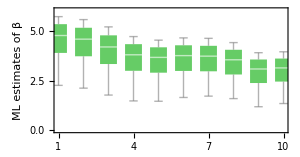

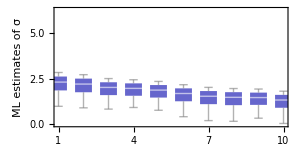

```mathematica
T//Dimensions
cl=ToString[#]&/@Range[1,10,1];
BoxWhiskerChart[
T⟦#⟧⟦All,1⟧&/@Range[1,10,1]
,PlotRange->{{1,10},{0,6.05}}
,ChartLabels->cl
,ImageSize->300
,LabelStyle->{FontSize->16,Black,FontFamily->"Arial"}
,FrameStyle->Directive[Thickness[0.004],Black]
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.525
,FrameLabel->{{"ML estimates of β",None},{"Percent FBS",None(*"n=8, σ=β/2"*)}}
,Axes->{False,False}
,AxesStyle->{Thickness[0.0035],Opacity[0.5,Gray]}
,ChartStyle->Opacity[0.6,Darker[Green]]
]

BoxWhiskerChart[
T⟦#⟧⟦All,2⟧&/@Range[1,10,1]
,PlotRange->{{1,10},{0,6.25}}
,ChartLabels->cl
,ImageSize->300
,LabelStyle->{FontSize->16,Black,FontFamily->"Arial"}
,FrameStyle->Directive[Thickness[0.004],Black]
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.5
,FrameLabel->{{"ML estimates of σ",None},{"Percent FBS",None(*"n=8, σ=β/2"*)}}
,Axes->{False,False}
,AxesStyle->{Thickness[0.0035],Opacity[0.5,Gray]}
,ChartStyle->Opacity[0.6,Darker[Blue]]
]
```

### Plotting the mean Growth rate differential r_C-r_D, of the fits to experiments of different serum concentration, as a function of y (fraction of C)

{4.77637,4.59273,4.19956,3.80477,3.67336,3.76322,3.73612,3.55377,3.08899,3.14302}

{2.30937,2.20139,2.01857,1.9667,1.87273,1.68722,1.53788,1.47864,1.46585,1.33226}

10

{RGBColor[0.5761666000000001, 0.8195192, 0.9884546],RGBColor[0.38027220000000006, 0.7144184, 0.9782062],RGBColor[0.27294619999999997, 0.5950244, 0.9451238],RGBColor[0.2541886, 0.4613372, 0.8892074],RGBColor[0.235431, 0.32765, 0.833291],RGBColor[0.26358420000000005, 0.2208948799999999, 0.7407537999999999],RGBColor[0.2917374, 0.11413976000000005, 0.6482166],RGBColor[0.27823319999999996, 0.04860975999999999, 0.5418926],RGBColor[0.22307160000000004, 0.024304880000000022, 0.42178180000000015],RGBColor[0.16791000000000006, 2.6983837386751476*^-17, 0.30167100000000013]}

22

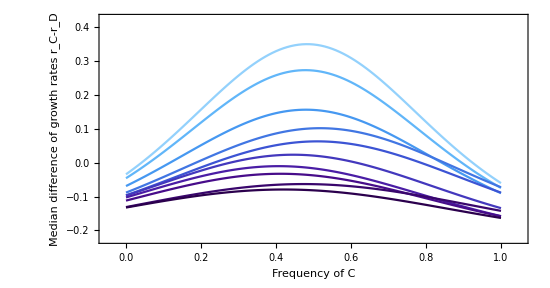

```mathematica
γ=1.0;
κ=0.25;


β=Median[T⟦#⟧⟦All,1⟧]&/@Range[1,10,1]
σ=Median[T⟦#⟧⟦All,2⟧]&/@Range[1,10,1]
Lσβ=Length[β]

rC[y_,β_,σ_,n_]:=γ If[n==0,1+ⅇ^σ,(1+ⅇ^σ)/(1+Exp[-(β (1+y(n-1))/n-σ)])]-κ;
rD[y_,β_,σ_,n_]:=γ If[n==0,1+ⅇ^σ,(1+ⅇ^σ)/(1+Exp[-(β (y(n-1))/n-σ)])];
colors=ColorData["DeepSeaColors"][1-#/0.1]&/@Range[0.01,0.1,0.01]
nMedian=Median[#&/@Range[4,40,1]]
ListPlot[
Table[
{y,rC[y,β⟦#⟧,σ⟦#⟧,nMedian]-rD[y,β⟦#⟧,σ⟦#⟧,nMedian]}
,{y,0,1,0.01}]&/@Range[1,Lσβ,1]
,PlotRange->{{-0.05,1.05},{-0.2-0.025,0.4+0.025}}
,Joined->True
,Frame->True
,PlotRange->All
,ImageSize->550
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}
,FrameStyle->Directive[Thickness[0.004],Black]
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.525
,FrameLabel->{{"Median difference 
of growth rates r_C-r_D",None},{"Frequency of C",None(*"n=8, σ=β/2"*)}}
,Axes->{True,False}
,AxesStyle->{Thickness[0.0035],Opacity[0.5,Gray]}
(*,PlotLegends->{Placed[{"n=15","n=25"},{0.8,0.75}]}*)
,PlotStyle->colors
]


scale={1,10};
BarLegend[
{colors,scale}
(*,LegendLabel->"Critical number of compartments SubscriptBox[StyleBox[\"N\",FontSlant->\"Italic\"], \"crit\"]"*)
,LabelStyle->{FontSize->20,FontFamily->"Arial",Black}
,LegendLayout->"Column"
,LegendMarkerSize->300
]
```

22

22

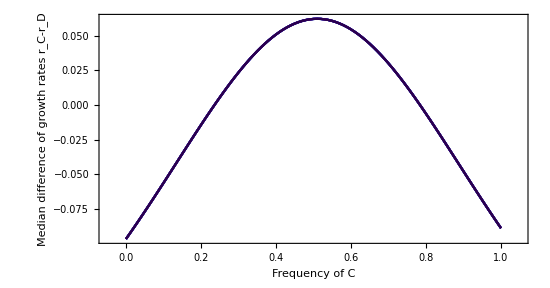

```mathematica
nn=Median[#&/@Range[4,40,1]]

Mean[#&/@Range[4,40,1]]

ListPlot[
Table[
{y,rC[y,3.67,1.87,nn]-rD[y,3.67,1.87,nn]}
,{y,0,1,0.01}]&/@Range[1,Lσβ,1]
,PlotRange->{{-0.05,1.05},All}
,Joined->True
,Frame->True
,PlotRange->All
,ImageSize->550
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}
,FrameStyle->Directive[Thickness[0.004],Black]
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.525
,FrameLabel->{{"Median difference 
of growth rates r_C-r_D",None},{"Frequency of C",None(*"n=8, σ=β/2"*)}}
,Axes->{True,False}
,AxesStyle->{Thickness[0.0035],Opacity[0.5,Gray]}
(*,PlotLegends->{Placed[{"n=15","n=25"},{0.8,0.75}]}*)
,PlotStyle->colors
]
```